```mathematica
fl[a_,b_,c_,d_,delta_,t_,n_]:=Sum[(UnitStep[t-k delta]-UnitStep[t-(k+1) delta]) (a[k]+b[k] (t-k delta)+c[k] (t-k delta)^2+d[k] (t-k delta)^3),{k,0,n}]
dfl[a_,b_,c_,d_,delta_,t_,n_]:=Sum[(UnitStep[t-k delta]-UnitStep[t-(k+1) delta]) (b[k]+2 c[k] (t-k delta)+3 d[k] (t-k delta)^2),{k,0,n}]
ddfl[a_,b_,c_,d_,delta_,t_,n_]:=Sum[(UnitStep[t-k delta]-UnitStep[t-(k+1) delta]) (2 c[k]+6 d[k] (t-k delta)),{k,0,n}]

n=4;
tmax=100;
delta=tmax/n;
eps=0.00001;
parms=beta->0.001;
u[y_]:=y^2-y^4

fl0=fl[a,b,c,d,delta,t,n];
dfl0=dfl[a,b,c,d,delta,t,n];
ddfl0=ddfl[a,b,c,d,delta,t,n];

For[k=n-1,k≥0,k--,fl0=fl0/.{a[k+1]->a[k]+delta b[k]+delta^2 c[k]+delta^3 d[k],b[k+1]->b[k]+2 delta c[k]+3 delta^2 d[k],c[k+1]->c[k]+3 delta d[k]};
dfl0=dfl0/.{a[k+1]->a[k]+delta b[k]+delta^2 c[k]+delta^3 d[k],b[k+1]->b[k]+2 delta c[k]+3 delta^2 d[k],c[k+1]->c[k]+3 delta d[k]};
ddfl0=ddfl0/.{a[k+1]->a[k]+delta b[k]+delta^2 c[k]+delta^3 d[k],b[k+1]->b[k]+2 delta c[k]+3 delta^2 d[k],c[k+1]->c[k]+3 delta d[k]}]

vars=Join[{a[0],b[0],c[0]},Table[d[k],{k,0,n}]];



dif=Integrate[dfl0^2+u[fl0]+beta/2 ddfl0^2,{t,0,tmax}]/.parms;
fl0i=(fl0/.{t->eps})==y0;
fl0d=(fl0/.{t->tmax-eps})==0;
dfl0i=(dfl0/.{t->eps})==0;
dfl0d=(dfl0/.{t->tmax-eps})==0;
bcs={fl0i,fl0d,dfl0i,dfl0d};
points=Table[dif,{t,0,tmax,delta/3}];
obj=points.points;
sol=NMinimize[Join[Join[{obj},bcs],{y0≥0.2}],Join[vars,{y0}],Method->"DifferentialEvolution"];
sol[[1]]
et=fl0/.parms/.sol[[2]];
gr1=Plot[et,{t,0,tmax},PlotRange->All,PlotStyle->{Thick,Blue}]
```

$Aborted

NMinimize::nnum: The function value 13 dif^2 is not a number at {a[0],b[0],c[0],d[0],d[1],d[2],d[3],d[4],«1»[x]} = {0.795769,-0.0000183482,0.917412,-0.0749438,0.212654,-0.304546,0.277116,0.987641,0.795769}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

{13 dif^2,a[0]+0.00001 b[0]+1.×10^-10 c[0]+1.×10^-15 d[0]==InterpolatingFunction[…][x],a[0]+25 b[0]+625 c[0]+15625 d[0]+625 (c[0]+75 d[0])+25 (b[0]+50 c[0]+1875 d[0])+15625 d[1]+625 (c[0]+75 d[0]+75 d[1])+25 (b[0]+50 c[0]+1875 d[0]+50 (c[0]+75 d[0])+1875 d[1])+15625 d[2]+625. (c[0]+75 d[0]+75 d[1]+75 d[2])+25. (b[0]+50 c[0]+1875 d[0]+50 (c[0]+75 d[0])+1875 d[1]+50 (c[0]+75 d[0]+75 d[1])+1875 d[2])+15625. d[3]==0,b[0]+0.00002 c[0]+3.×10^-10 d[0]==0,b[0]+50 c[0]+1875 d[0]+50 (c[0]+75 d[0])+1875 d[1]+50 (c[0]+75 d[0]+75 d[1])+1875 d[2]+50. (c[0]+75 d[0]+75 d[1]+75 d[2])+1875. d[3]==0,InterpolatingFunction[…][x]≥0.2}

ReplaceAll::reps: {a[0],b[0],c[0],d[0],d[1],d[2],d[3],d[4],«1»[x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {a[0],b[0],c[0],d[0],d[1],d[2],d[3],d[4],«1»[x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

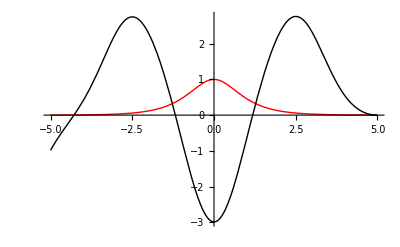

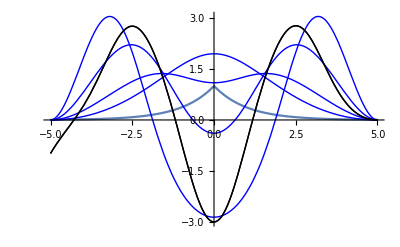

```mathematica
Clear[V,dV,y1,y0]
V[x_]:=-2 x+4 x^3;
dV[x_]:=-2+12 x^2

y0=Exp[-Abs[x]];
beta=5;
xmax=5;
nmax=5;
bcs={y1[-xmax]==0,y1[xmax]==0,y1'[-xmax]==0,y1'[xmax]==0};
SOLS={Plot[y0,{x,-xmax,xmax}, PlotRange->All]};
thickness=Thin;
color=Blue;

For[k=1,k≤nmax,k++,ode=y1''[x]+V[y0]+dV[y0] (y1[x]-y0)-beta y1''''[x];
sol=NDSolve[Join[{ode==0},bcs],y1,{x,-xmax,xmax}][[1]];
y0=y1[x]/.sol;
If[k==nmax,thickness=Thick;color=Black];
AppendTo[SOLS,Plot[y0,{x,-xmax,xmax},PlotStyle->{thickness,color}, PlotRange->All]]]

grfin=SOLS[[Length[SOLS]]];
Show[Plot[Sqrt[1-Tanh[Sqrt[2] x]^2],{x,-xmax,xmax},PlotStyle->{Thick,Red}, PlotRange->All],grfin]
Show[SOLS,grfin,PlotRange->All]
```